```mathematica
a=b=c=1/4;
d=d;
l=a*b*c;
m=a+b+c;
β0=d ;
β1=1/12*(m+5*l-23*a*b*c+5)-3*β0;
β2=1/12*(-8*m+8*l+16*a*b*c-16)+3*β0 ;
β3=1/12*(-5*m-l-5*a*b*c+23)-β0;
α0=a*b*c;
α1=-(l+a*b*c);
α2=m+l;
α3=-(m+1);
α4=1;
ρ[z_]:=α0+α1 z+α2 z^2+α3 z^3+α4 z^4;
σ[z_]:=β0+β1 z+β2 z^2+β3 z^3;
zz=Exp[I ξ];
μ=ρ[zz]/σ[zz]
μ/.ξ->π
```

(1/64-ⅇ^(ⅈ ξ)/32+49/64 ⅇ^(2 ⅈ ξ)-7/4 ⅇ^(3 ⅈ ξ)+ⅇ^(4 ⅈ ξ))/(d+(175/384-3 d) ⅇ^(ⅈ ξ)+(-173/96+3 d) ⅇ^(2 ⅈ ξ)+(613/384-d) ⅇ^(3 ⅈ ξ))

57/(16 (-185/48+8 d))

```mathematica
-210/769
```

-210/769

```mathematica
Manipulate[
ParametricPlot[{Re[μ],Im[μ]}/.d->α0
,{ξ,0,2π}
,MaxRecursion->3
,PlotPoints-> 100
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All]
,{α0,-0.25,0.8}
]
```

```mathematica
A={α0,α1,α2,α3,α4,0};
B={β0,β1,β2,β3,0};
k=4;p=3;
C111=1/((p+1)!)(∑_(i=0)^k A[[i+1]]*i^(p+1)-(p+1)*∑_(i=0)^k B[[i+1]]*i^p)/(∑_(i=0)^k B[[i+1]])(*C*)
```

1/6 (4047/32-4 (175/384+27 (613/384-d)-3 d+8 (-173/96+3 d)))

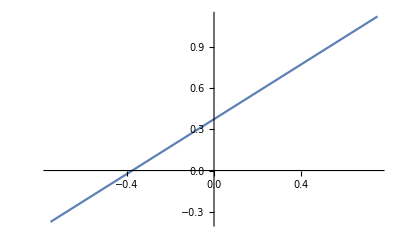

```mathematica
Plot[3/8+d,{d,-3/4,3/4}]
```

```mathematica
2/(-11/3+8 d)
```

2/(-11/3+8 d)

```mathematica
Simplify[2/(-11/3+8 d)]
```

```mathematica
6/(-11+24 d)
```

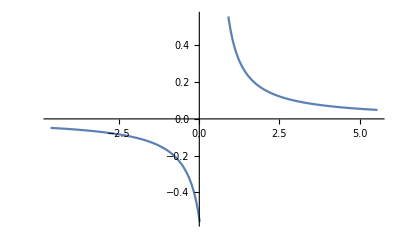

```mathematica
Plot[6/(-11+24 d),{d,-4.641666666666667,5.558333333333334}]
```

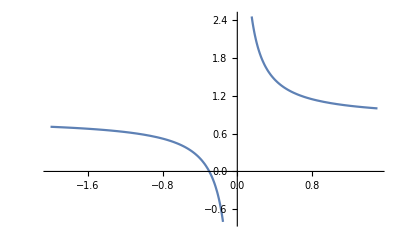

```mathematica
Plot[5/6+1/(4 d),{d,-2,1.5009000000000001}]
```

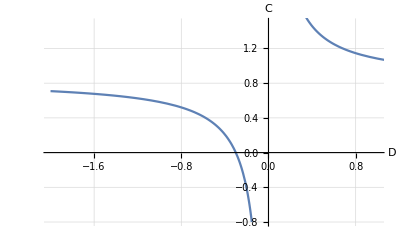

```mathematica
Show[%55,PlotLabel->None,LabelStyle->{12,GrayLevel[0]},GridLines->Automatic,PlotRange->{{-2,1},{-0.8,1.5}},LabelStyle->{13,GrayLevel[0]},GridLines->Automatic,AxesLabel->{Style[D,Medium],Style[C,Medium]},AxesStyle->{{Arrowheads[0.04],AbsoluteThickness[1]}, {Arrowheads[0.04],AbsoluteThickness[1]}}](*a=b=c=0*)
```

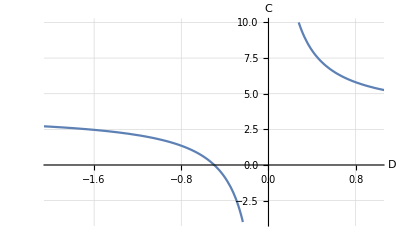

```mathematica
Plot[229/64+57/(32 a),{a,-2.491561183043802,2.491561183043802},LabelStyle->{12,GrayLevel[0]},GridLines->Automatic,PlotRange->{{-2,1},{-4,10}},LabelStyle->{13,GrayLevel[0]},GridLines->Automatic,AxesLabel->{Style[D,Medium],Style[C,Medium]},AxesStyle->{{Arrowheads[0.04],AbsoluteThickness[1]}, {Arrowheads[0.04],AbsoluteThickness[1]}}]
```